```mathematica
dataDrDiGe519t=Import["C:\\DrDiGe\\DrDiGe\\dr-di-ge-519.csv"]
```

```mathematica
edgesDrDiGe519= Map[#[[1]]->#[[2]]&,dataDrDiGe519t]
```

```mathematica
weightsDrDiGe519 = Map[#[[3]] &, dataDrDiGe519t]
```

```mathematica
gDrDiGe519=UndirectedGraph[edgesDrDiGe519, EdgeWeight->  weightsDrDiGe519]
```

```mathematica
CommunityGraphPlot[gDrDiGe519,Method->{"Hierarchical","Weighted"->True},ImageSize->1200,VertexSize->Larger,PlotLabel->Style["DrugBank 5.1.9 DDSN network based on gene-disease",FontSize->18],CommunityRegionStyle->LightGray,CommunityLabels->{"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39","40","41","42","43","44","45","46","47","48","49","50","51","52","53","54","55","56","57","58","59","60","61","62","63","64","65","66","67","68","69","70","71","72","73","74","75","76","77","78","79","80"}]
```

-Graphics-

```mathematica
cg1=FindGraphCommunities[gDrDiGe519]
```

{{Lidocaine,Dronedarone,Felodipine,Isoflurane,Ascorbic acid,Verapamil,Loperamide,Polyethylene glycol 400,Bepridil,Artenimol,Tamoxifen,Carvedilol,Calcium Phosphate,Calcium phosphate dihydrate,Calcium citrate,Terazosin,Phenylalanine,Tyrosine,Levocarnitine,Perhexiline,Metyrosine,Droxidopa,Norepinephrine,Sapropterin,Nicotine,Disulfiram,Pentolinium,Amantadine,Levacetylmethadol,Bupropion,Methadone,Levamisole,Dextromethorphan,Fluoxetine,Varenicline,Haloperidol,Etomidate,Clevidipine,Cinnarizine,Ketoconazole,Dequalinium,Nimodipine,Zonisamide,Fluvoxamine,Disopyramide,Procainamide,Doxepin,Astemizole,Ibutilide,Vernakalant,Chlorobutanol,Erythromycin,Prazosin,Amsacrine,Cisapride,Dofetilide,Flecainide,Isavuconazole,Quinidine,Potassium nitrate,Pitolisant,Clarithromycin,Ciprofloxacin,Thioridazine,Halofantrine,Sertindole,Pentoxyverine,Propafenone,Sotalol,Phenytoin,Terfenadine,Nefazodone,Hydroxyzine,Chlorpromazine,Imipramine,Pimozide,Loratadine,Indecainide,Mexiletine,Cinchocaine,Riluzole,Ajmaline,Tocainide,Mephenytoin,Moricizine,Encainide,Fosphenytoin,Prilocaine,Ethotoin,Benzonatate,Hexylcaine,Metergoline,Bethanidine,Glymidine,Glimepiride,Tolbutamide,Acetohexamide,Repaglinide,Gliclazide,Nateglinide,Chlorpropamide,Levosimendan,Glipizide,Gliquidone,Lauric acid,Milrinone,Aminophylline,Enoximone,Theophylline,Cilostazol,Oxtriphylline,Anagrelide,Amrinone,Ziprasidone,Apraclonidine,Bromocriptine,Phenoxybenzamine,Oxymetazoline,Clozapine,Rotigotine,Yohimbine,Fenoldopam,Metamfetamine,Risperidone,Quetiapine,Mianserin,Brimonidine,Methotrimeprazine,Epinephrine,Asenapine,Paliperidone,Loxapine,Racepinephrine,Guanfacine,Xylometazoline,Aripiprazole lauroxil,Cabergoline,Apomorphine,Trimipramine,Clonidine,Aripiprazole,Celiprolol,Tolazoline,Guanabenz,Pizotifen,Lisuride,Phenacemide,Nitrazepam,Permethrin,Phenazopyridine,Trifluoperazine,Levamlodipine,Diltiazem,Mavacamten,Etidronic acid,Nilvadipine,Nifedipine,Nicardipine,Clodronic acid,Nisoldipine,Propiverine,Norelgestromin,Phenol,Cefotaxime,Guaiacol,Silver,Patent Blue,Pamidronic acid,Risedronic acid,Zoledronic acid,Alendronic acid,Ibandronate,Trimethadione,Methsuximide,Flunarizine,Manidipine,Ethosuximide,Desipramine,Allopurinol,Febuxostat,Melatonin,Promethazine,Perphenazine,Calcium levulinate,Prenylamine,Fluphenazine,Phenformin,Nicorandil,Neomycin,Cinacalcet,Etelcalcetide,Glycolic acid},{Catumaxomab,Amivantamab,Foreskin keratinocyte (neonatal),Fostamatinib,Zanubrutinib,Denileukin diftitox,Tremelimumab,Pentostatin,Abatacept,Mosunetuzumab,Tofacitinib,Ipilimumab,Pazopanib,Baricitinib,Copanlisib,Cladribine,Dipyridamole,Arsenic trioxide,Nintedanib,Teplizumab,Aldesleukin,Dasatinib,Blinatumomab,Muromonab,Didanosine,Streptozocin,Umbralisib,Abrocitinib,Caffeine,Auranofin,Ponatinib,Basiliximab,Ruxolitinib,Leuprolide,Ganirelix,Erdafitinib,Nafarelin,Regorafenib,Selpercatinib,Futibatinib,Lenvatinib,Triptorelin,Infigratinib,Pralsetinib,Danazol,Palifermin,Degarelix,Histrelin,Linzagolix,Elagolix,Gonadorelin,Cetrorelix,Relugolix,Pemigatinib,Goserelin,Buserelin,Tivozanib,Abarelix,Sorafenib,Darbepoetin alfa,Nitrous acid,Voxelotor,Peginesatide,Ferrous ascorbate,Erythropoietin,Ferric pyrophosphate citrate,Iron,Ferrous sulfate anhydrous,Sodium ferric gluconate complex,Ferrous fumarate,Ferric derisomaltose,Pentaerythritol tetranitrate,Ferrous gluconate,Ferrous glycine sulfate,Iron Dextran,Ferrous succinate,Sargramostim,Foreskin fibroblast (neonatal),Sitaxentan,Teriflunomide,Glasdegib,Leflunomide,Atovaquone,Halcinonide,Macitentan,Alpelisib,Sonidegib,Ambrisentan,Bosentan,Vismodegib,Ritodrine,Hyaluronidase (ovine),Hyaluronidase (human recombinant),Hyaluronidase,Becaplermin,Nilotinib,Ancestim,Midostaurin,Sunitinib,Imatinib,Olaratumab,Ripretinib,Avapritinib,Pexidartinib,Celecoxib,Oseltamivir,Axitinib,Ubidecarenone,Carboxin,Cabozantinib,Roxadustat,Hexachlorophene,Belzutifan,Aluminum chloride,Amitriptyline,alpha-Tocopherol succinate,Cholecystokinin,D-alpha-Tocopherol acetate,Adenine,5-O-phosphono-alpha-D-ribofuranosyl diphosphate,Citric acid,Dantrolene,Tetracaine,Clofarabine,Dibotermin alfa,Tasonermin,Fludarabine,Carfilzomib,Mifamurtide,Rilonacept,Nelarabine,Lacosamide,Larotrectinib,Entrectinib,Rufinamide,Cenegermin,Zidovudine,Bosutinib,Trametinib,Dabrafenib,Binimetinib,Vemurafenib,Encorafenib,Adagrasib,Selumetinib,Sotorasib,Cobimetinib,Ampicillin,Chloramphenicol,Inebilizumab,Tafasitamab,Loncastuximab tesirine,Lisocabtagene maraleucel,Brexucabtagene autoleucel,Tisagenlecleucel,Axicabtagene ciloleucel,Palbociclib,Trilaciclib,Abemaciclib,Ribociclib,Cisplatin,Isoflurophate,Doxapram,Asciminib,Mercaptopurine,Tirbanibulin,Tepotinib,Capmatinib,Crizotinib,Ingenol mebutate,Hypromellose,Technetium Tc-99m nofetumomab merpentan,Lorlatinib,Gilteritinib,Ceritinib,Alectinib,Deucravacitinib},{Lepirudin,Dabigatran etexilate,Drotrecogin alfa,Zinc acetate,Human C1-esterase inhibitor,Copper,Enoxaparin,Coagulation Factor IX Human,Menadione,Thrombomodulin Alfa,Zinc,Turoctocog alfa,Conestat alfa,Coagulation Factor IX (Recombinant),Anti-inhibitor coagulant complex,Antithrombin Alfa,Argatroban,Turoctocog alfa pegol,Bivalirudin,Proflavine,Kappadione,Ximelagatran,Cetuximab,Gemtuzumab ozogamicin,Sutimlimab,Alefacept,Bevacizumab,Benralizumab,Zinc chloride,Sarilumab,Palivizumab,Zinc sulfate, unspecified form,Human immunoglobulin G,Alemtuzumab,Etanercept,Heparin,Alteplase,Urokinase,Reteplase,Tranexamic acid,Ancrod,Tenecteplase,Streptokinase,Thrombin,Prothrombin,Aprotinin,Aminocaproic acid,Human thrombin,Thrombin alfa,Anistreplase,Clove oil,Antihemophilic factor, human recombinant,Edoxaban,Moroctocog alfa,Lonoctocog alfa,Coagulation factor VIIa Recombinant Human,Coagulation factor VII human,Emicizumab,Albutrepenonacog alfa,Protein S human,Bemiparin,Betrixaban,Nonacog beta pegol,Protamine sulfate,Apixaban,Fondaparinux,Rivaroxaban,Antihemophilic factor human,Eculizumab,Pegcetacoplan,Ravulizumab,Anisindione,Phylloquinone,Collagenase clostridium histolyticum,Aducanumab,Deferoxamine,Dimercaprol,Migalastat,Von Willebrand factor human,Flutemetamol (18F),Florbetaben (18F),Vonicog alfa,Tromethamine,Florbetapir (18F),Sodium tetradecyl sulfate,Diethylstilbestrol,Ezogabine,Flavone,Protein C,Damoctocog alfa pegol,Rurioctocog alfa pegol,Ecallantide,Lanadelumab,Berotralstat,Flavin adenine dinucleotide,Dopamine,Ribostamycin,Glutathione,Minocycline,Dichloroacetic acid,Glycerin,Nicotinamide,Stiripentol,Phenprocoumon,Cupric Chloride,Phenindione,Warfarin,Dicoumarol,Acenocoumarol,Ardeparin,Sulodexide,Nadroparin,Antithrombin III human,Dalteparin,Tinzaparin,Danaparoid,Tetracycline,Alirocumab,Inclisiran,Evolocumab,Porfimer sodium,Catridecacog,Benzoic acid,Isoprenaline,Ibrutinib,Acalabrutinib,Polatuzumab vedotin,Vorinostat,Ocriplasmin,Volanesorsen,Ethanolamine oleate,Tafamidis,Tegafur-uracil,Gimeracil},{Brigatinib,Acetylcysteine,Insulin human,Thyroid, porcine,Liotrix,Dextrothyroxine,Levothyroxine,Liothyronine,Meprobamate,Levetiracetam,Insulin detemir,Azathioprine,Halothane,Chromic chloride,Vigabatrin,Flavin mononucleotide,Nitrendipine,Thiopental,Topiramate,Sevoflurane,Aspartic acid,Amlodipine,Eflornithine,Gabapentin enacarbil,Zolpidem,Phenelzine,Glycine,Botulinum toxin type B,Quinidine barbiturate,Pyridoxal phosphate,Insulin beef,Insulin glargine,Methoxyflurane,Insulin pork,Pyruvic acid,Ethanol,Lamotrigine,Atropine,D-Serine,Nandrolone decanoate,Desflurane,Insulin aspart,Insulin degludec,Talbutal,Vitamin E,Somatrem,Primidone,Glutamic acid,Eszopiclone,Isradipine,Pentobarbital,Gabapentin,Zopiclone,Carisoprodol,Cannabidiol,Methylphenobarbital,Taurine,Ginkgo biloba,Mecasermin rinfabate,Mecasermin,Secobarbital,Enflurane,Butobarbital,Butalbital,Carboxymethylcellulose,Flumazenil,Sildenafil,Teprotumumab,Amobarbital,Valproic acid,Insulin glulisine,Insulin lispro,Lindane,Abciximab,Ferric maltol,Eptifibatide,Tirofiban,Antithymocyte immunoglobulin (rabbit),Ademetionine,Cysteine,Methyldopa,Ornithine,Carbidopa,Benserazide,Mitapivat,Asparagine,Temsirolimus,Memantine,Orphenadrine,Everolimus,Sirolimus,Dalfampridine,Propanoic acid,Amifampridine,Esketamine,Methyprylon,Phenobarbital,Glutethimide,Lumateperone,Pimecrolimus,Bioallethrin,Meperidine,Amoxapine,Thiamylal,Butabarbital,Fluciclovine (18F),Lithium carbonate,Zaleplon,Felbamate,Lithium citrate,Propofol,Fospropofol,gamma-Hydroxybutyric acid,Cisatracurium,Fomepizole,Benzoyl peroxide,Sodium oxybate},{Aluminium,Aluminum acetate,Aluminium phosphate,NADH,Succinic acid,Chlormerodrin,Captopril,Trichlormethiazide,Hydroflumethiazide,Acetazolamide,Hexylresorcinol,Hydroquinone,Manganese,Ribavirin,Mycophenolic acid,Dorzolamide,Vitamin A,Azelaic acid,Xanthinol,Benzthiazide,Diclofenamide,Omega-3-carboxylic acids,Vardenafil,Tadalafil,Mycophenolate mofetil,Monobenzone,Bendroflumethiazide,Arbutin,Brinzolamide,Methazolamide,Sodium carbonate,Tretinoin,Metformin,Voretigene neparvovec,Palmitic Acid,Hyaluronic acid,Ramipril,Cilazapril,Lisinopril,Benazepril,Spirapril,Rescinnamine,Fosinopril,Quinapril,Moexipril,Zofenopril,Enalaprilat,Trandolapril,Perindopril,Enalapril,Tramadol,Ouabain,Amylmetacresol,Torasemide,Quinethazone,Piretanide,Potassium chloride,Etacrynic acid,Furosemide,Chlorthalidone,Diazoxide,Sodium sulfate,Sulpiride,Urea,Chlorothiazide,Cyclothiazide,Valdecoxib,Ethinamate,Sulthiame,Digoxin,Magnesium acetate,Digitoxin,Potassium,Potassium acetate,Potassium cation,Potassium sulfate,Deslanoside,Acetyldigitoxin,Almitrine,Ciclopirox,Magnesium cation,Bretylium,Metolazone,Indapamide,Polythiazide,Hydrochlorothiazide,Finasteride,Dutasteride,Oleic Acid,Tyloxapol,Glycyrrhizic acid},{Gestrinone,Fluocinonide,Spironolactone,Tetracosactide,Hydrocortisone valerate,Bremelanotide,Corticotropin,Fluoxymesterone,Hydrocortisone acetate,Hydrocortisone phosphate,Hydrocortisone cypionate,Hydrocortisone probutate,Progesterone,Hydrocortisone butyrate,Dexamethasone,Dexamethasone acetate,Seractide acetate,Flunisolide,Triamcinolone,Loteprednol etabonate,Fluticasone furoate,Prednicarbate,Norethisterone,Prednisolone,Ulipristal,Levonorgestrel,Desoximetasone,Ulobetasol,Ciclesonide,Mometasone furoate,Betamethasone,Megestrol acetate,Flumethasone,Clobetasol propionate,Fluocinolone acetonide,Hydrocortisone,Hydrocortamate,Difluprednate,Fluorometholone,Mifepristone,Desonide,Betamethasone phosphate,Segesterone acetate,Clocortolone,Prednisone,Flurandrenolide,Amcinonide,Clobetasone,Prednisolone phosphate,Methylprednisolone,Medrysone,Cortisone acetate,Drospirenone,Prednisolone acetate,Fluticasone propionate,Difluocortolone,Diflorasone,Fludrocortisone,Beclomethasone dipropionate,Budesonide,Alclometasone,Deflazacort,Fluticasone,Tixocortol,Rimexolone,Testosterone enanthate,Eplerenone,Testosterone cypionate,Testosterone,Finerenone,Desoxycorticosterone acetate,Procaine,Azacitidine,Flucytosine,Decitabine},{Mesalazine,Acetylsalicylic acid,Idelalisib,Dexibuprofen,Crofelemer,Ivacaftor,Sulfinpyrazone,Lumacaftor,Tezacaftor,Ibuprofen,Glyburide,Elexacaftor,Icosapent,Ketorolac,Glycol salicylate,Oxaprozin,Troglitazone,Loxoprofen,Lumiracoxib,Dexketoprofen,Phenylbutazone,Phenyl salicylate,Rosiglitazone,Suprofen,Ketoprofen,Lornoxicam,Tiaprofenic acid,Nabumetone,Trolamine salicylate,Diflunisal,Etodolac,Acetaminophen,Naproxen,Sulindac,Metamizole,Antipyrine,Flurbiprofen,Balsalazide,Bendazac,Acemetacin,Diclofenac,Salsalate,Diethylcarbamazine,Meloxicam,Choline magnesium trisalicylate,Piroxicam,Indomethacin,Tolfenamic acid,Carprofen,Mefenamic acid,Minoxidil,Flufenamic acid,Meclofenamic acid,Bromfenac,Antrafenine,Tolmetin,Salicylic acid,Aceclofenac,Nepafenac,Menthyl salicylate,Bufexamac,Fenoprofen,Triflusal,Sulfasalazine,Tenoxicam,Amiloride,Triamterene,Clotrimazole,Quinine,Pseudoephedrine,Papaverine},{Calcitriol,Dihydrotachysterol,Alfacalcidol,Paricalcitol,Vitamin D,Ergocalciferol,Doxercalciferol,Calcifediol,Calcipotriol,Cholesterol,Cholecalciferol,Curcumin},{Neratinib,Dacomitinib,Necitumumab,Mobocertinib,Panitumumab,Osimertinib,Erlotinib,Vandetanib,Gefitinib,Afatinib,Lapatinib},{Pegfilgrastim,Ibalizumab,Lipegfilgrastim,Filgrastim,Lenograstim,Plerixafor,Framycetin,Eflapegrastim,Alpha-1-proteinase inhibitor,Baclofen,gamma-Aminobutyric acid},{Desmopressin,Lypressin,Terlipressin,Conivaptan,Vasopressin,Atosiban,Tolvaptan,Demeclocycline},{Thyrotropin alfa,2-mercaptobenzothiazole,Resorcinol,Methimazole,Triclosan,Carbimazole,Propylthiouracil},{Cyanocobalamin,Methionine,Biotin,Valine,Mecobalamin,Thimerosal,Hydroxocobalamin},{Abiraterone,Levoketoconazole,Aminoglutethimide,Mitotane,Osilodrostat,Metyrapone},{Menotropins,Corifollitropin alfa,Follitropin,Choriogonadotropin alfa,Urofollitropin},{Canagliflozin,Empagliflozin,Ertugliflozin,Sotagliflozin,Dapagliflozin},{Adenosine phosphate,Dyphylline,Iloprost,Crisaborole},{Acarbose,Miglitol,alpha-Arbutin,Scopolamine},{Romiplostim,Avatrombopag,Lusutrombopag,Eltrombopag},{Vincristine,Cabazitaxel,Podofilox},{Erythrityl tetranitrate,Nesiritide,Vosoritide},{Duvelisib,Bumetanide},{Sermorelin,Tesamorelin},{Botulinum toxin type A,Letibotulinumtoxina},{Choline,Choline salicylate},{Creatine,Guanidine},{Griseofulvin,Anthralin},{Lenalidomide,Denosumab},{Albendazole,Mebendazole},{Methotrexate,Pemetrexed},{Ivosidenib,Olutasidenib},{Methoxy polyethylene glycol-epoetin beta},{Ziconotide},{Methohexital}}

```mathematica
distanceMatrix=GraphDistanceMatrix[gDrDiGe519];

averagePathLength=Mean[Flatten[distanceMatrix]];
```

```mathematica
averagePathLength
```

∞

```mathematica
components=ConnectedComponents[gDrDiGe519];
```

```mathematica
%26
```

{{Lepirudin,Dabigatran etexilate,Drotrecogin alfa,Zinc acetate,Human C1-esterase inhibitor,Copper,Enoxaparin,Coagulation Factor IX Human,Menadione,Thrombomodulin Alfa,Zinc,Turoctocog alfa,Conestat alfa,Coagulation Factor IX (Recombinant),Anti-inhibitor coagulant complex,Antithrombin Alfa,Argatroban,Turoctocog alfa pegol,Bivalirudin,Proflavine,Kappadione,Ximelagatran,Fostamatinib,Heparin,Thrombin,Human thrombin,Thrombin alfa,Protein S human,Nonacog beta pegol,Valproic acid,Artenimol,Von Willebrand factor human,Vonicog alfa,Sodium tetradecyl sulfate,Calcium Phosphate,Diethylstilbestrol,Calcium phosphate dihydrate,Ezogabine,Calcium citrate,Flavone,Protein C,Damoctocog alfa pegol,Rurioctocog alfa pegol,Cetuximab,Brigatinib,Bevacizumab,Palivizumab,Human immunoglobulin G,Pazopanib,Nintedanib,Dasatinib,Acetylsalicylic acid,Erdafitinib,Regorafenib,Lenvatinib,Tivozanib,Sorafenib,Alteplase,Reteplase,Ancrod,Tenecteplase,Prothrombin,Anistreplase,Darbepoetin alfa,Nitrous acid,Peginesatide,Erythropoietin,Ferric pyrophosphate citrate,Iron,Ferrous sulfate anhydrous,Sodium ferric gluconate complex,Methoxy polyethylene glycol-epoetin beta,Pentaerythritol tetranitrate,Iron Dextran,Insulin human,Bemiparin,Eculizumab,Ravulizumab,Meprobamate,Levetiracetam,Insulin detemir,Felodipine,Azathioprine,Halothane,Ziconotide,Vigabatrin,Flavin mononucleotide,Nitrendipine,Thiopental,Topiramate,Isoflurane,Sevoflurane,Aspartic acid,Amlodipine,Gabapentin enacarbil,Zolpidem,Phenelzine,Glycine,Botulinum toxin type B,Quinidine barbiturate,Pyridoxal phosphate,Insulin beef,Insulin glargine,Methoxyflurane,Insulin pork,Pyruvic acid,Ethanol,Lamotrigine,Atropine,D-Serine,Nandrolone decanoate,Desflurane,Insulin aspart,Ascorbic acid,Insulin degludec,Talbutal,Vitamin E,Somatrem,Primidone,Glutamic acid,Eszopiclone,Verapamil,Isradipine,Pentobarbital,Gabapentin,Zopiclone,Carisoprodol,Cannabidiol,Methylphenobarbital,Taurine,Ginkgo biloba,Mecasermin,Secobarbital,Enflurane,Butobarbital,Butalbital,Carboxymethylcellulose,Flumazenil,Sildenafil,Amobarbital,Insulin glulisine,Insulin lispro,Lindane,Bepridil,Collagenase clostridium histolyticum,Deferoxamine,Aluminium,Carvedilol,Dimercaprol,Migalastat,Flutemetamol (18F),Florbetaben (18F),Tromethamine,Florbetapir (18F),Ecallantide,Sunitinib,Imatinib,Pexidartinib,Celecoxib,Oseltamivir,Axitinib,Flavin adenine dinucleotide,Dopamine,Ribostamycin,Roxadustat,Hexachlorophene,Thiamylal,Glutathione,Minocycline,Captopril,Manganese,Ibutilide,Isavuconazole,Glymidine,Glimepiride,Tolbutamide,Repaglinide,Gliclazide,Nateglinide,Chlorpropamide,Levosimendan,Glipizide,Diazoxide,Gliquidone,Lauric acid,Ardeparin,Sulodexide,Cisplatin,Isoflurophate,Tetracycline,Catridecacog,Benzoic acid,Isoprenaline,Ibrutinib,Acalabrutinib,Polatuzumab vedotin,Vorinostat,Ocriplasmin,Ethanolamine oleate,Tafamidis,Sutimlimab,Zinc chloride,Zinc sulfate, unspecified form,Zanubrutinib,Selpercatinib,Voxelotor,Ferrous ascorbate,Ferrous fumarate,Ferric derisomaltose,Ferrous gluconate,Ferrous glycine sulfate,Ferrous succinate,Pegcetacoplan,Eflornithine,Mecasermin rinfabate,Teprotumumab,Aducanumab,Aluminum acetate,Aluminium phosphate,Lanadelumab,Berotralstat,Volanesorsen,Acetylcysteine,Ponatinib,Leuprolide,Ganirelix,Nafarelin,Triptorelin,Danazol,Palifermin,Degarelix,Histrelin,Gonadorelin,Cetrorelix,Goserelin,Buserelin,Abarelix,Urokinase,Tranexamic acid,Streptokinase,Aprotinin,Aminocaproic acid,Fondaparinux,Cysteine,NADH,Trichlormethiazide,Hydroflumethiazide,Acetazolamide,Ribavirin,Mycophenolic acid,Dorzolamide,Vitamin A,Xanthinol,Nicotinamide,Benzthiazide,Dequalinium,Diclofenamide,Vardenafil,Tadalafil,Mycophenolate mofetil,Bendroflumethiazide,Brinzolamide,Methazolamide,Zonisamide,Stiripentol,Tretinoin,Palmitic Acid,Hyaluronic acid,Nadroparin,Dalteparin,Tinzaparin,Danaparoid,Futibatinib,Infigratinib,Pralsetinib,Gestrinone,Linzagolix,Elagolix,Relugolix,Pemigatinib,Protamine sulfate,Aluminum chloride,Sodium carbonate,Voretigene neparvovec,Antithrombin III human,Antihemophilic factor, human recombinant,Coagulation factor VIIa Recombinant Human,Edoxaban,Moroctocog alfa,Lonoctocog alfa,Coagulation factor VII human,Emicizumab,Albutrepenonacog alfa,Betrixaban,Apixaban,Rivaroxaban,Antihemophilic factor human,Anisindione,Phylloquinone,Phenprocoumon,Cupric Chloride,Phenindione,Warfarin,Dicoumarol,Acenocoumarol,Neratinib,Dacomitinib,Necitumumab,Catumaxomab,Panitumumab,Erlotinib,Foreskin keratinocyte (neonatal),Vandetanib,Gefitinib,Afatinib,Lidocaine,Lapatinib,Denileukin diftitox,Duvelisib,Pentostatin,Abatacept,Tofacitinib,Baricitinib,Cladribine,Dipyridamole,Mesalazine,Arsenic trioxide,Teplizumab,Aldesleukin,Muromonab,Didanosine,Caffeine,Auranofin,Basiliximab,Ruxolitinib,Idelalisib,Foreskin fibroblast (neonatal),Chromic chloride,Loperamide,Sitaxentan,Teriflunomide,Glasdegib,Leflunomide,Atovaquone,Macitentan,Tamoxifen,Sonidegib,Fluocinonide,Ambrisentan,Bosentan,Vismodegib,Ritodrine,Becaplermin,Nilotinib,Ancestim,Olaratumab,Ubidecarenone,Carboxin,Cabozantinib,Dextromethorphan,Temsirolimus,Memantine,Orphenadrine,Everolimus,Sirolimus,Dalfampridine,Propanoic acid,Amitriptyline,Methohexital,Esketamine,Methyprylon,Phenobarbital,Glutethimide,Lumateperone,Pimecrolimus,Meperidine,Amoxapine,Haloperidol,Zaleplon,Felbamate,Etomidate,Dexibuprofen,Crofelemer,Ivacaftor,Lumacaftor,Tezacaftor,Bumetanide,Ibuprofen,Glyburide,Sulfasalazine,Cholecystokinin,Citric acid,Phenytoin,Amiloride,Triamterene,Dibotermin alfa,Lacosamide,Urea,Entrectinib,Rufinamide,Zidovudine,Bosutinib,Dabrafenib,Binimetinib,Vemurafenib,Encorafenib,Selumetinib,Cobimetinib,Ampicillin,Palbociclib,Abemaciclib,Doxapram,Tirbanibulin,Capmatinib,Crizotinib,Ingenol mebutate,Ceritinib,Alectinib,Mobocertinib,Osimertinib,Amivantamab,Tremelimumab,Mosunetuzumab,Ipilimumab,Copanlisib,Blinatumomab,Umbralisib,Abrocitinib,Halcinonide,Alpelisib,Midostaurin,Ripretinib,Avapritinib,Belzutifan,Bioallethrin,Elexacaftor,Larotrectinib,Cenegermin,Trametinib,Adagrasib,Sotorasib,Trilaciclib,Ribociclib,Asciminib,Tepotinib,Lorlatinib,Gilteritinib,Deucravacitinib,Liothyronine,Succinic acid,Thyroid, porcine,Liotrix,Dextrothyroxine,Levothyroxine,Dronedarone,Chlormerodrin,Ornithine,Clevidipine,Cinnarizine,Nimodipine,Amsacrine,Trifluoperazine,Levamlodipine,Diltiazem,Etidronic acid,Nilvadipine,Nifedipine,Nicardipine,Clodronic acid,Nisoldipine,Norelgestromin,Phenol,Cefotaxime,Guaiacol,Glycolic acid,Mavacamten,Propiverine,Silver,Patent Blue,Clove oil,Chlorpromazine,Pimozide,Cinchocaine,Phenoxybenzamine,Flunarizine,Melatonin,Promethazine,Perphenazine,Prenylamine,Fluphenazine,Neomycin,Cinacalcet,Calcium levulinate,Etelcalcetide,Gemtuzumab ozogamicin,Alefacept,Benralizumab,Sarilumab,Alemtuzumab,Etanercept,Icosapent,Ketorolac,Phenylbutazone,Suprofen,Nabumetone,Diflunisal,Etodolac,Acetaminophen,Naproxen,Sulindac,Flurbiprofen,Diclofenac,Diethylcarbamazine,Meloxicam,Piroxicam,Indomethacin,Carprofen,Mefenamic acid,Minoxidil,Meclofenamic acid,Tolmetin,Salicylic acid,Fenoprofen,Tenoxicam,Glycol salicylate,Oxaprozin,Loxoprofen,Lumiracoxib,Dexketoprofen,Phenyl salicylate,Ketoprofen,Lornoxicam,Tiaprofenic acid,Trolamine salicylate,Metamizole,Antipyrine,Balsalazide,Bendazac,Acemetacin,Salsalate,Choline magnesium trisalicylate,Tolfenamic acid,Flufenamic acid,Bromfenac,Antrafenine,Aceclofenac,Nepafenac,Menthyl salicylate,Bufexamac,Triflusal,Polyethylene glycol 400,Levocarnitine,Spironolactone,Progesterone,Clobetasol propionate,Fluticasone propionate,Fludrocortisone,Eplerenone,Testosterone,Fluticasone furoate,Drospirenone,Fluticasone,Testosterone enanthate,Testosterone cypionate,Finerenone,Desoxycorticosterone acetate,Clotrimazole,Quinine,Ouabain,Tegafur-uracil,Gimeracil,Butabarbital,Fluciclovine (18F),Quinethazone,Furosemide,Sodium sulfate,Sulpiride,Chlorothiazide,Cyclothiazide,Valdecoxib,Ethinamate,Sulthiame,Amifampridine,Asparagine,Desipramine,gamma-Aminobutyric acid,Sulfinpyrazone,Disopyramide,Procainamide,Flecainide,Quinidine,Propafenone,Indecainide,Mexiletine,Riluzole,Tocainide,Mephenytoin,Moricizine,Encainide,Fosphenytoin,Prilocaine,Ethotoin,Benzonatate,Hexylcaine,Vernakalant,Ajmaline,Ademetionine,Methyldopa,Phenylalanine,Tyrosine,Carbidopa,Benserazide,Mitapivat,Nicotine,Methadone,Levamisole,Fluoxetine,Propofol,Pentolinium,Amantadine,Levacetylmethadol,Bupropion,Varenicline,Lithium carbonate,Lithium citrate,Fospropofol,gamma-Hydroxybutyric acid,Cisatracurium,Disulfiram,alpha-Tocopherol succinate,D-alpha-Tocopherol acetate,Fluvoxamine,Astemizole,Erythromycin,Prazosin,Cisapride,Dofetilide,Ciprofloxacin,Sotalol,Terfenadine,Hydroxyzine,Imipramine,Loratadine,Trimethadione,Ethosuximide,Terazosin,Perhexiline,Ketoconazole,Doxepin,Chlorobutanol,Potassium nitrate,Pitolisant,Clarithromycin,Thioridazine,Halofantrine,Sertindole,Pentoxyverine,Nefazodone,Methsuximide,Manidipine,Abiraterone,Levoketoconazole,Fomepizole,Benzoyl peroxide,Etacrynic acid,Digoxin,Deslanoside,Acetyldigitoxin,Ciclopirox,Bretylium,Magnesium acetate,Digitoxin,Potassium,Potassium acetate,Potassium cation,Potassium sulfate,Almitrine,Magnesium cation,Norepinephrine,Ziprasidone,Apraclonidine,Oxymetazoline,Clozapine,Fenoldopam,Risperidone,Brimonidine,Epinephrine,Loxapine,Guanfacine,Cabergoline,Apomorphine,Trimipramine,Clonidine,Tolazoline,Guanabenz,Lisuride,Droxidopa,Bromocriptine,Rotigotine,Yohimbine,Metamfetamine,Quetiapine,Mianserin,Methotrimeprazine,Asenapine,Paliperidone,Racepinephrine,Xylometazoline,Aripiprazole lauroxil,Aripiprazole,Celiprolol,Pizotifen,Allopurinol,Febuxostat,Phenformin,Nicorandil,Dichloroacetic acid,Glycerin,Ramipril,Lisinopril,Benazepril,Rescinnamine,Fosinopril,Quinapril,Moexipril,Trandolapril,Perindopril,Enalapril,Cilazapril,Spirapril,Zofenopril,Enalaprilat,Bethanidine,Acetohexamide,Milrinone,Theophylline,Anagrelide,Aminophylline,Enoximone,Cilostazol,Oxtriphylline,Amrinone,Alirocumab,Evolocumab,Porfimer sodium,Inclisiran,Tetracosactide,Hexylresorcinol,Hydroquinone,Hydrocortisone valerate,Bremelanotide,Azelaic acid,Corticotropin,Omega-3-carboxylic acids,Fluoxymesterone,Hydrocortisone acetate,Monobenzone,Arbutin,Hydrocortisone phosphate,Hydrocortisone cypionate,Hydrocortisone probutate,Metformin,Hydrocortisone butyrate,Dexamethasone,Dexamethasone acetate,Seractide acetate,Metolazone,Indapamide,Hydrochlorothiazide,Polythiazide,Torasemide,Potassium chloride,Chlorthalidone,Piretanide,Tramadol,Amylmetacresol,Metergoline,Phenacemide,Nitrazepam,Permethrin,Phenazopyridine,Oleic Acid,Flunisolide,Triamcinolone,Loteprednol etabonate,Prednicarbate,Norethisterone,Prednisolone,Ulipristal,Levonorgestrel,Desoximetasone,Ulobetasol,Ciclesonide,Betamethasone,Megestrol acetate,Flumethasone,Fluocinolone acetonide,Hydrocortisone,Hydrocortamate,Difluprednate,Fluorometholone,Mifepristone,Desonide,Clocortolone,Prednisone,Flurandrenolide,Amcinonide,Methylprednisolone,Medrysone,Cortisone acetate,Difluocortolone,Diflorasone,Beclomethasone dipropionate,Budesonide,Alclometasone,Tixocortol,Rimexolone,Mometasone furoate,Betamethasone phosphate,Segesterone acetate,Clobetasone,Prednisolone phosphate,Prednisolone acetate,Deflazacort,Hypromellose,Technetium Tc-99m nofetumomab merpentan,Sargramostim,Hyaluronidase (ovine),Hyaluronidase (human recombinant),Hyaluronidase,Streptozocin,Chloramphenicol,Inebilizumab,Tafasitamab,Loncastuximab tesirine,Lisocabtagene maraleucel,Brexucabtagene autoleucel,Tisagenlecleucel,Axicabtagene ciloleucel,Clofarabine,Tasonermin,Fludarabine,Carfilzomib,Mifamurtide,Rilonacept,Nelarabine,Papaverine,Dantrolene,Tetracaine,Pseudoephedrine,Adenine,5-O-phosphono-alpha-D-ribofuranosyl diphosphate,Thyrotropin alfa,Carbimazole,2-mercaptobenzothiazole,Resorcinol,Methimazole,Triclosan,Propylthiouracil,Abciximab,Eptifibatide,Antithymocyte immunoglobulin (rabbit),Ferric maltol,Tirofiban,Alendronic acid,Troglitazone,Rosiglitazone,Cyanocobalamin,Biotin,Valine,Hydroxocobalamin,Procaine,Baclofen,Azacitidine,Flucytosine,Decitabine,Metyrosine,Sapropterin,Sodium oxybate,Aminoglutethimide,Mitotane,Metyrapone,Osilodrostat,Finasteride,Dutasteride,Tyloxapol,Glycyrrhizic acid,Mercaptopurine,Pamidronic acid,Zoledronic acid,Risedronic acid,Ibandronate,Methionine,Mecobalamin,Thimerosal,Pegfilgrastim,Filgrastim,Alpha-1-proteinase inhibitor,Ibalizumab,Lipegfilgrastim,Lenograstim,Plerixafor,Framycetin,Eflapegrastim},{Calcitriol,Dihydrotachysterol,Alfacalcidol,Paricalcitol,Vitamin D,Ergocalciferol,Doxercalciferol,Calcifediol,Calcipotriol,Cholesterol,Cholecalciferol,Curcumin},{Desmopressin,Lypressin,Terlipressin,Conivaptan,Vasopressin,Atosiban,Tolvaptan,Demeclocycline},{Canagliflozin,Empagliflozin,Ertugliflozin,Sotagliflozin,Dapagliflozin},{Menotropins,Corifollitropin alfa,Follitropin,Choriogonadotropin alfa,Urofollitropin},{Romiplostim,Avatrombopag,Lusutrombopag,Eltrombopag},{Acarbose,Miglitol,alpha-Arbutin,Scopolamine},{Adenosine phosphate,Dyphylline,Iloprost,Crisaborole},{Erythrityl tetranitrate,Nesiritide,Vosoritide},{Vincristine,Cabazitaxel,Podofilox},{Ivosidenib,Olutasidenib},{Methotrexate,Pemetrexed},{Albendazole,Mebendazole},{Lenalidomide,Denosumab},{Griseofulvin,Anthralin},{Creatine,Guanidine},{Choline,Choline salicylate},{Botulinum toxin type A,Letibotulinumtoxina},{Sermorelin,Tesamorelin}}

```mathematica
largestComponentVertices=First[MaximalBy[components,Length]];
```

```mathematica
%28
```

{Lepirudin,Dabigatran etexilate,Drotrecogin alfa,Zinc acetate,Human C1-esterase inhibitor,Copper,Enoxaparin,Coagulation Factor IX Human,Menadione,Thrombomodulin Alfa,Zinc,Turoctocog alfa,Conestat alfa,Coagulation Factor IX (Recombinant),Anti-inhibitor coagulant complex,Antithrombin Alfa,Argatroban,Turoctocog alfa pegol,Bivalirudin,Proflavine,Kappadione,Ximelagatran,Fostamatinib,Heparin,Thrombin,Human thrombin,Thrombin alfa,Protein S human,Nonacog beta pegol,Valproic acid,Artenimol,Von Willebrand factor human,Vonicog alfa,Sodium tetradecyl sulfate,Calcium Phosphate,Diethylstilbestrol,Calcium phosphate dihydrate,Ezogabine,Calcium citrate,Flavone,Protein C,Damoctocog alfa pegol,Rurioctocog alfa pegol,Cetuximab,Brigatinib,Bevacizumab,Palivizumab,Human immunoglobulin G,Pazopanib,Nintedanib,Dasatinib,Acetylsalicylic acid,Erdafitinib,Regorafenib,Lenvatinib,Tivozanib,Sorafenib,Alteplase,Reteplase,Ancrod,Tenecteplase,Prothrombin,Anistreplase,Darbepoetin alfa,Nitrous acid,Peginesatide,Erythropoietin,Ferric pyrophosphate citrate,Iron,Ferrous sulfate anhydrous,Sodium ferric gluconate complex,Methoxy polyethylene glycol-epoetin beta,Pentaerythritol tetranitrate,Iron Dextran,Insulin human,Bemiparin,Eculizumab,Ravulizumab,Meprobamate,Levetiracetam,Insulin detemir,Felodipine,Azathioprine,Halothane,Ziconotide,Vigabatrin,Flavin mononucleotide,Nitrendipine,Thiopental,Topiramate,Isoflurane,Sevoflurane,Aspartic acid,Amlodipine,Gabapentin enacarbil,Zolpidem,Phenelzine,Glycine,Botulinum toxin type B,Quinidine barbiturate,Pyridoxal phosphate,Insulin beef,Insulin glargine,Methoxyflurane,Insulin pork,Pyruvic acid,Ethanol,Lamotrigine,Atropine,D-Serine,Nandrolone decanoate,Desflurane,Insulin aspart,Ascorbic acid,Insulin degludec,Talbutal,Vitamin E,Somatrem,Primidone,Glutamic acid,Eszopiclone,Verapamil,Isradipine,Pentobarbital,Gabapentin,Zopiclone,Carisoprodol,Cannabidiol,Methylphenobarbital,Taurine,Ginkgo biloba,Mecasermin,Secobarbital,Enflurane,Butobarbital,Butalbital,Carboxymethylcellulose,Flumazenil,Sildenafil,Amobarbital,Insulin glulisine,Insulin lispro,Lindane,Bepridil,Collagenase clostridium histolyticum,Deferoxamine,Aluminium,Carvedilol,Dimercaprol,Migalastat,Flutemetamol (18F),Florbetaben (18F),Tromethamine,Florbetapir (18F),Ecallantide,Sunitinib,Imatinib,Pexidartinib,Celecoxib,Oseltamivir,Axitinib,Flavin adenine dinucleotide,Dopamine,Ribostamycin,Roxadustat,Hexachlorophene,Thiamylal,Glutathione,Minocycline,Captopril,Manganese,Ibutilide,Isavuconazole,Glymidine,Glimepiride,Tolbutamide,Repaglinide,Gliclazide,Nateglinide,Chlorpropamide,Levosimendan,Glipizide,Diazoxide,Gliquidone,Lauric acid,Ardeparin,Sulodexide,Cisplatin,Isoflurophate,Tetracycline,Catridecacog,Benzoic acid,Isoprenaline,Ibrutinib,Acalabrutinib,Polatuzumab vedotin,Vorinostat,Ocriplasmin,Ethanolamine oleate,Tafamidis,Sutimlimab,Zinc chloride,Zinc sulfate, unspecified form,Zanubrutinib,Selpercatinib,Voxelotor,Ferrous ascorbate,Ferrous fumarate,Ferric derisomaltose,Ferrous gluconate,Ferrous glycine sulfate,Ferrous succinate,Pegcetacoplan,Eflornithine,Mecasermin rinfabate,Teprotumumab,Aducanumab,Aluminum acetate,Aluminium phosphate,Lanadelumab,Berotralstat,Volanesorsen,Acetylcysteine,Ponatinib,Leuprolide,Ganirelix,Nafarelin,Triptorelin,Danazol,Palifermin,Degarelix,Histrelin,Gonadorelin,Cetrorelix,Goserelin,Buserelin,Abarelix,Urokinase,Tranexamic acid,Streptokinase,Aprotinin,Aminocaproic acid,Fondaparinux,Cysteine,NADH,Trichlormethiazide,Hydroflumethiazide,Acetazolamide,Ribavirin,Mycophenolic acid,Dorzolamide,Vitamin A,Xanthinol,Nicotinamide,Benzthiazide,Dequalinium,Diclofenamide,Vardenafil,Tadalafil,Mycophenolate mofetil,Bendroflumethiazide,Brinzolamide,Methazolamide,Zonisamide,Stiripentol,Tretinoin,Palmitic Acid,Hyaluronic acid,Nadroparin,Dalteparin,Tinzaparin,Danaparoid,Futibatinib,Infigratinib,Pralsetinib,Gestrinone,Linzagolix,Elagolix,Relugolix,Pemigatinib,Protamine sulfate,Aluminum chloride,Sodium carbonate,Voretigene neparvovec,Antithrombin III human,Antihemophilic factor, human recombinant,Coagulation factor VIIa Recombinant Human,Edoxaban,Moroctocog alfa,Lonoctocog alfa,Coagulation factor VII human,Emicizumab,Albutrepenonacog alfa,Betrixaban,Apixaban,Rivaroxaban,Antihemophilic factor human,Anisindione,Phylloquinone,Phenprocoumon,Cupric Chloride,Phenindione,Warfarin,Dicoumarol,Acenocoumarol,Neratinib,Dacomitinib,Necitumumab,Catumaxomab,Panitumumab,Erlotinib,Foreskin keratinocyte (neonatal),Vandetanib,Gefitinib,Afatinib,Lidocaine,Lapatinib,Denileukin diftitox,Duvelisib,Pentostatin,Abatacept,Tofacitinib,Baricitinib,Cladribine,Dipyridamole,Mesalazine,Arsenic trioxide,Teplizumab,Aldesleukin,Muromonab,Didanosine,Caffeine,Auranofin,Basiliximab,Ruxolitinib,Idelalisib,Foreskin fibroblast (neonatal),Chromic chloride,Loperamide,Sitaxentan,Teriflunomide,Glasdegib,Leflunomide,Atovaquone,Macitentan,Tamoxifen,Sonidegib,Fluocinonide,Ambrisentan,Bosentan,Vismodegib,Ritodrine,Becaplermin,Nilotinib,Ancestim,Olaratumab,Ubidecarenone,Carboxin,Cabozantinib,Dextromethorphan,Temsirolimus,Memantine,Orphenadrine,Everolimus,Sirolimus,Dalfampridine,Propanoic acid,Amitriptyline,Methohexital,Esketamine,Methyprylon,Phenobarbital,Glutethimide,Lumateperone,Pimecrolimus,Meperidine,Amoxapine,Haloperidol,Zaleplon,Felbamate,Etomidate,Dexibuprofen,Crofelemer,Ivacaftor,Lumacaftor,Tezacaftor,Bumetanide,Ibuprofen,Glyburide,Sulfasalazine,Cholecystokinin,Citric acid,Phenytoin,Amiloride,Triamterene,Dibotermin alfa,Lacosamide,Urea,Entrectinib,Rufinamide,Zidovudine,Bosutinib,Dabrafenib,Binimetinib,Vemurafenib,Encorafenib,Selumetinib,Cobimetinib,Ampicillin,Palbociclib,Abemaciclib,Doxapram,Tirbanibulin,Capmatinib,Crizotinib,Ingenol mebutate,Ceritinib,Alectinib,Mobocertinib,Osimertinib,Amivantamab,Tremelimumab,Mosunetuzumab,Ipilimumab,Copanlisib,Blinatumomab,Umbralisib,Abrocitinib,Halcinonide,Alpelisib,Midostaurin,Ripretinib,Avapritinib,Belzutifan,Bioallethrin,Elexacaftor,Larotrectinib,Cenegermin,Trametinib,Adagrasib,Sotorasib,Trilaciclib,Ribociclib,Asciminib,Tepotinib,Lorlatinib,Gilteritinib,Deucravacitinib,Liothyronine,Succinic acid,Thyroid, porcine,Liotrix,Dextrothyroxine,Levothyroxine,Dronedarone,Chlormerodrin,Ornithine,Clevidipine,Cinnarizine,Nimodipine,Amsacrine,Trifluoperazine,Levamlodipine,Diltiazem,Etidronic acid,Nilvadipine,Nifedipine,Nicardipine,Clodronic acid,Nisoldipine,Norelgestromin,Phenol,Cefotaxime,Guaiacol,Glycolic acid,Mavacamten,Propiverine,Silver,Patent Blue,Clove oil,Chlorpromazine,Pimozide,Cinchocaine,Phenoxybenzamine,Flunarizine,Melatonin,Promethazine,Perphenazine,Prenylamine,Fluphenazine,Neomycin,Cinacalcet,Calcium levulinate,Etelcalcetide,Gemtuzumab ozogamicin,Alefacept,Benralizumab,Sarilumab,Alemtuzumab,Etanercept,Icosapent,Ketorolac,Phenylbutazone,Suprofen,Nabumetone,Diflunisal,Etodolac,Acetaminophen,Naproxen,Sulindac,Flurbiprofen,Diclofenac,Diethylcarbamazine,Meloxicam,Piroxicam,Indomethacin,Carprofen,Mefenamic acid,Minoxidil,Meclofenamic acid,Tolmetin,Salicylic acid,Fenoprofen,Tenoxicam,Glycol salicylate,Oxaprozin,Loxoprofen,Lumiracoxib,Dexketoprofen,Phenyl salicylate,Ketoprofen,Lornoxicam,Tiaprofenic acid,Trolamine salicylate,Metamizole,Antipyrine,Balsalazide,Bendazac,Acemetacin,Salsalate,Choline magnesium trisalicylate,Tolfenamic acid,Flufenamic acid,Bromfenac,Antrafenine,Aceclofenac,Nepafenac,Menthyl salicylate,Bufexamac,Triflusal,Polyethylene glycol 400,Levocarnitine,Spironolactone,Progesterone,Clobetasol propionate,Fluticasone propionate,Fludrocortisone,Eplerenone,Testosterone,Fluticasone furoate,Drospirenone,Fluticasone,Testosterone enanthate,Testosterone cypionate,Finerenone,Desoxycorticosterone acetate,Clotrimazole,Quinine,Ouabain,Tegafur-uracil,Gimeracil,Butabarbital,Fluciclovine (18F),Quinethazone,Furosemide,Sodium sulfate,Sulpiride,Chlorothiazide,Cyclothiazide,Valdecoxib,Ethinamate,Sulthiame,Amifampridine,Asparagine,Desipramine,gamma-Aminobutyric acid,Sulfinpyrazone,Disopyramide,Procainamide,Flecainide,Quinidine,Propafenone,Indecainide,Mexiletine,Riluzole,Tocainide,Mephenytoin,Moricizine,Encainide,Fosphenytoin,Prilocaine,Ethotoin,Benzonatate,Hexylcaine,Vernakalant,Ajmaline,Ademetionine,Methyldopa,Phenylalanine,Tyrosine,Carbidopa,Benserazide,Mitapivat,Nicotine,Methadone,Levamisole,Fluoxetine,Propofol,Pentolinium,Amantadine,Levacetylmethadol,Bupropion,Varenicline,Lithium carbonate,Lithium citrate,Fospropofol,gamma-Hydroxybutyric acid,Cisatracurium,Disulfiram,alpha-Tocopherol succinate,D-alpha-Tocopherol acetate,Fluvoxamine,Astemizole,Erythromycin,Prazosin,Cisapride,Dofetilide,Ciprofloxacin,Sotalol,Terfenadine,Hydroxyzine,Imipramine,Loratadine,Trimethadione,Ethosuximide,Terazosin,Perhexiline,Ketoconazole,Doxepin,Chlorobutanol,Potassium nitrate,Pitolisant,Clarithromycin,Thioridazine,Halofantrine,Sertindole,Pentoxyverine,Nefazodone,Methsuximide,Manidipine,Abiraterone,Levoketoconazole,Fomepizole,Benzoyl peroxide,Etacrynic acid,Digoxin,Deslanoside,Acetyldigitoxin,Ciclopirox,Bretylium,Magnesium acetate,Digitoxin,Potassium,Potassium acetate,Potassium cation,Potassium sulfate,Almitrine,Magnesium cation,Norepinephrine,Ziprasidone,Apraclonidine,Oxymetazoline,Clozapine,Fenoldopam,Risperidone,Brimonidine,Epinephrine,Loxapine,Guanfacine,Cabergoline,Apomorphine,Trimipramine,Clonidine,Tolazoline,Guanabenz,Lisuride,Droxidopa,Bromocriptine,Rotigotine,Yohimbine,Metamfetamine,Quetiapine,Mianserin,Methotrimeprazine,Asenapine,Paliperidone,Racepinephrine,Xylometazoline,Aripiprazole lauroxil,Aripiprazole,Celiprolol,Pizotifen,Allopurinol,Febuxostat,Phenformin,Nicorandil,Dichloroacetic acid,Glycerin,Ramipril,Lisinopril,Benazepril,Rescinnamine,Fosinopril,Quinapril,Moexipril,Trandolapril,Perindopril,Enalapril,Cilazapril,Spirapril,Zofenopril,Enalaprilat,Bethanidine,Acetohexamide,Milrinone,Theophylline,Anagrelide,Aminophylline,Enoximone,Cilostazol,Oxtriphylline,Amrinone,Alirocumab,Evolocumab,Porfimer sodium,Inclisiran,Tetracosactide,Hexylresorcinol,Hydroquinone,Hydrocortisone valerate,Bremelanotide,Azelaic acid,Corticotropin,Omega-3-carboxylic acids,Fluoxymesterone,Hydrocortisone acetate,Monobenzone,Arbutin,Hydrocortisone phosphate,Hydrocortisone cypionate,Hydrocortisone probutate,Metformin,Hydrocortisone butyrate,Dexamethasone,Dexamethasone acetate,Seractide acetate,Metolazone,Indapamide,Hydrochlorothiazide,Polythiazide,Torasemide,Potassium chloride,Chlorthalidone,Piretanide,Tramadol,Amylmetacresol,Metergoline,Phenacemide,Nitrazepam,Permethrin,Phenazopyridine,Oleic Acid,Flunisolide,Triamcinolone,Loteprednol etabonate,Prednicarbate,Norethisterone,Prednisolone,Ulipristal,Levonorgestrel,Desoximetasone,Ulobetasol,Ciclesonide,Betamethasone,Megestrol acetate,Flumethasone,Fluocinolone acetonide,Hydrocortisone,Hydrocortamate,Difluprednate,Fluorometholone,Mifepristone,Desonide,Clocortolone,Prednisone,Flurandrenolide,Amcinonide,Methylprednisolone,Medrysone,Cortisone acetate,Difluocortolone,Diflorasone,Beclomethasone dipropionate,Budesonide,Alclometasone,Tixocortol,Rimexolone,Mometasone furoate,Betamethasone phosphate,Segesterone acetate,Clobetasone,Prednisolone phosphate,Prednisolone acetate,Deflazacort,Hypromellose,Technetium Tc-99m nofetumomab merpentan,Sargramostim,Hyaluronidase (ovine),Hyaluronidase (human recombinant),Hyaluronidase,Streptozocin,Chloramphenicol,Inebilizumab,Tafasitamab,Loncastuximab tesirine,Lisocabtagene maraleucel,Brexucabtagene autoleucel,Tisagenlecleucel,Axicabtagene ciloleucel,Clofarabine,Tasonermin,Fludarabine,Carfilzomib,Mifamurtide,Rilonacept,Nelarabine,Papaverine,Dantrolene,Tetracaine,Pseudoephedrine,Adenine,5-O-phosphono-alpha-D-ribofuranosyl diphosphate,Thyrotropin alfa,Carbimazole,2-mercaptobenzothiazole,Resorcinol,Methimazole,Triclosan,Propylthiouracil,Abciximab,Eptifibatide,Antithymocyte immunoglobulin (rabbit),Ferric maltol,Tirofiban,Alendronic acid,Troglitazone,Rosiglitazone,Cyanocobalamin,Biotin,Valine,Hydroxocobalamin,Procaine,Baclofen,Azacitidine,Flucytosine,Decitabine,Metyrosine,Sapropterin,Sodium oxybate,Aminoglutethimide,Mitotane,Metyrapone,Osilodrostat,Finasteride,Dutasteride,Tyloxapol,Glycyrrhizic acid,Mercaptopurine,Pamidronic acid,Zoledronic acid,Risedronic acid,Ibandronate,Methionine,Mecobalamin,Thimerosal,Pegfilgrastim,Filgrastim,Alpha-1-proteinase inhibitor,Ibalizumab,Lipegfilgrastim,Lenograstim,Plerixafor,Framycetin,Eflapegrastim}

```mathematica
largestComponentGraph=Subgraph[gDrDiGe519,largestComponentVertices];
```

```mathematica
%30
```

```mathematica
distanceMatrix=GraphDistanceMatrix[largestComponentGraph];
```

```mathematica
averagePathLength=Mean[Flatten[distanceMatrix]];
```

```mathematica
3.1236050199702405
```

3.12361

```mathematica
mcc =MeanClusteringCoefficient[gDrDiGe519]
```

3889379647047019504230042621843081984902631172494525832345514437/4606438123852905584396796334661588621880972502626974427352680000

```mathematica
N[mcc];
```

```mathematica
0.84433558911975
```

0.844336

```mathematica
averageDegree=Mean[VertexDegree[gDrDiGe519]];
```

```mathematica
16843/485
```

16843/485

```mathematica
N[averageDegree]
```

34.7278

```mathematica
weightedDegrees=Total[WeightedAdjacencyMatrix[gDrDiGe519]];
```

```mathematica
%44
```

{42,28,57,383,73,731,59,59,67,46,312,59,55,113,92,66,28,58,40,34,65,29,47,21,11,22,18,39,284,37,27,28,13,25,27,47,24,14,253,103,12,24,347,400,25,54,23,98,11,27,15,118,24,85,38,36,30,188,96,31,21,50,132,23,102,97,44,112,39,169,26,57,84,36,195,56,41,4,64,21,88,39,240,52,32,100,70,38,184,59,168,194,219,289,46,81,92,42,84,47,237,85,63,59,46,48,41,117,145,53,58,103,50,110,27,10,22,9,16,21,13,39,19,21,13,33,26,19,1,1,22,40,53,27,78,46,78,124,50,48,31,67,51,47,64,72,49,74,86,9,10,10,11,11,12,9,10,12,11,10,67,9,16,25,46,32,12,17,13,36,35,234,16,11,32,26,31,35,39,42,32,31,31,47,57,35,53,46,30,45,35,30,9,6,9,425,178,108,214,111,181,125,14,143,227,232,129,312,227,102,148,198,130,142,192,201,173,90,173,243,130,158,149,108,102,186,129,106,128,109,114,132,353,106,208,106,135,248,214,192,353,202,163,134,176,234,244,196,136,143,150,111,109,129,107,190,162,175,202,168,118,169,208,24,127,140,151,321,5,5,6,5,5,10,7,7,8,7,8,8,9,8,8,53,39,43,204,60,32,36,48,40,93,49,119,51,58,39,27,31,29,59,105,6,23,18,59,16,43,51,32,15,45,38,11,11,9,12,11,7,89,16,82,21,69,36,15,17,23,8,9,10,88,3,3,6,11,17,31,21,31,39,26,32,96,91,24,60,28,61,5,6,16,177,6,3,71,45,40,10,8,4,5,34,5,97,4,4,8,1,29,3,36,52,43,5,37,1,1,20,19,2,26,13,17,36,19,27,47,18,64,93,29,42,209,15,4,3,3,3,3,3,11,11,15,14,24,16,25,18,22,21,19,22,8,31,90,76,45,119,136,93,113,131,28,93,12,88,102,102,89,106,94,96,84,113,132,19,22,155,5,95,93,5,134,15,7,2,25,3,111,28,31,16,28,24,44,82,34,24,1,1,82,97,85,60,12,7,5,56,8,51,53,36,66,118,57,12,14,10,54,6,78,58,103,112,65,54,3,85,54,129,57,62,7,79,8,95,74,70,73,187,13,190,201,96,6,55,1,52,64,81,130,146,14,55,72,84,84,68,4,124,64,102,77,64,3,98,80,87,95,64,79,82,87,108,203,83,90,167,108,94,74,87,74,108,77,78,110,86,84,76,95,88,88,83,85,84,88,71,84,94,98,72,92,102,78,118,95,3,13,3,6,6,9,10,5,8,2,3,10,46,74,90,56,92,348,430,134,179,106,108,147,61,94,158,105,130,84,88,98,99,82,93,94,133,71,163,98,77,103,114,97,128,102,29,18,19,29,22,19,21,18,39,23,37,52,54,35,153,113,95,190,182,94,119,105,89,100,109,103,75,96,68,99,112,138,89,109,194,322,170,302,118,116,128,102,182,89,124,128,202,166,210,283,147,280,162,180,171,166,143,149,150,122,145,138,58,38,132,177,72,82,227,79,83,71,112,117,73,133,26,76,11,11,65,22,21,2,3,33,66,23,20,43,53,13,9,27,30,33,6,40,21,37,26,114,26,104,63,54,34,27,48,46,38,57,52,37,7,2,7,14,11,17,23,26,190,70,91,156,117,119,64,85,82,59,133,120,49,194,82,68,87,94,193,148,119,78,171,151,82,78,96,124,151,141,83,82,92,7,37,7,7,7,3,5,70,45,55,61,58,54,94,115,59,37,49,42,41,46,66,66,51,61,59,40,19,16,16,16,13,17,21,19,13,4,7,7,9,7,5,3,4,2,17,20,58,15,14,1,2,72,78,67,151,190,94,94,107,87,138,99,153,121,40,52,106,51,70,38,53,61,48,56,60,14,41,49,36,39,31,35,3,3,103,29,91,20,20,19,15,9,3,10,10,18,19,3,3,15,14,10,19,26,23,30,22,43,42,51,51,41,48,2,2,14,17,5,18,27,26,4,4,12,4,12,2,2,1,13,1,1,9,10,30,13,8,20,5,3,4,4,5,4,6,5,6,9,7,2,17,19,27,7,27,1,22,22,29,36,6,15,32,45,37,1,14,5,6,7,11,6,6,2,1,3,3,2,1,23,4,24,5,3,3,3,3,6,15,11,8,13,7,5,7,6,5,1,1}

```mathematica
degreeDistribution=Tally[weightedDegrees];
```

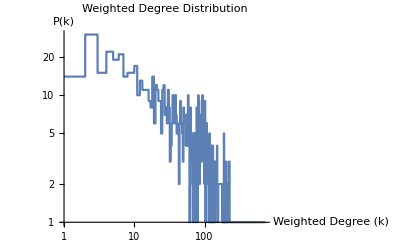

```mathematica
LogLogPlot[Interpolation[degreeDistribution,InterpolationOrder->0][x],{x,Min[degreeDistribution[[All,1]]],Max[degreeDistribution[[All,1]]]},PlotLabel->"Weighted Degree Distribution",AxesLabel->{"Weighted Degree (k)","P(k)"}]
```

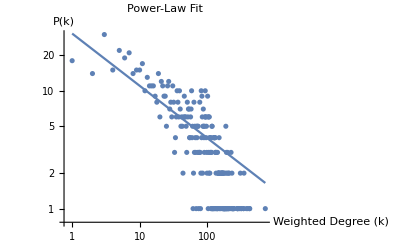

```mathematica
fit=FindFit[degreeDistribution,a*x^(-gamma),{a,gamma},x];
powerLawExponent=gamma/. fit;
Show[ListLogLogPlot[degreeDistribution],LogLogPlot[a*x^(-gamma)/. fit,{x,Min[degreeDistribution[[All,1]]],Max[degreeDistribution[[All,1]]]}],PlotLabel->"Power-Law Fit",AxesLabel->{"Weighted Degree (k)","P(k)"},PlotLegends->{"Data","Power-Law Fit"}]
```

```mathematica
fit
```

{a→30.5817,gamma→0.442631}